```mathematica
(*
e[x]_here = e_1(x)_{Lagrangian approach};
v[x]_here = {v^1(x)}_{Lagrangian approach};
σ[x]_here  = σ(x)_{Lagrangian approach};
*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
ass={ψ[x]∈Reals};
```

```mathematica
e[x_]:={Cos[ψ[x]],-Sin[ψ[x]]}
```

```mathematica
n[x_]:={-e[x][[2]],e[x][[1]]}/Norm[e[x]]
```

```mathematica
g[x_]:=Simplify[{{e[x].e[x]}},Assumptions->ass]
```

```mathematica
sqrtdetg[x_]:=Sqrt[Det[g[x]]]
```

```mathematica
gc[x_]:=Inverse[g[x]]
```

```mathematica
FullSimplify[{{-n'[x].e[x]}},Assumptions->ass]
```

{{-ψ'[x]}}

```mathematica
b[x_]:={{-ψ'[x]}}
```

```mathematica
1/2FullSimplify[Sum[gc[x][[i,j]]b[x][[j,i]],{i,1,1},{j,1,1}],Assumptions->ass]
```

-1/2 ψ'[x]

```mathematica
H[x_]:=-1/2 ψ'[x]
```

```mathematica
K[x_]:=0
```

```mathematica
Γ[x_]:={{{0}}}
```

```mathematica
eqv=FullSimplify[ρ(v[x]v'[x]-2 v[x]w[x]b[x][[1,1]]-w[x]w'[x])
-gc[x][[1,1]]σ'[x]
-2 η(v''[x] - (w'[x]b[x][[1,1]]+w[x] b'[x][[1,1]]))==0,Assumptions->ass];
eqw={w[x]==0};
eqσ=FullSimplify[v'[x]-2 H[x]w[x]==0,Assumptions->ass];
eqψ=FullSimplify[{ρ v[x](v[x]b[x][[1,1]]+w'[x])
-κ( - 2 H''[x]-4H[x](H[x]^2-K[x]))
-2 σ[x]H[x]
- 2η( v'[x]b[x][[1,1]]-2 w[x]*(2 H[x]^2-K[x]))==0},Assumptions->ass];

eqX={X1'[x]==Cos[ψ[x]],X2'[x]==-Sin[ψ[x]]};
```

```mathematica
(*the ODEs above imply that v[x]=vc, and σ[x]=σc (independent of x), and because I am at steady state, it must be w[x]=0, thus I simplify the equations by setting *)
```

```mathematica
v[x_]:=vc
w[x_]:=0
σ[x_]:=σc
```

```mathematica
eqs=FullSimplify[Flatten[{eqψ,eqX}]]
```

{2 (vc^2 ρ-σc) ψ'[x]+κ ψ'[x]^3+2 κ ψ^(3)[x]==0,Cos[ψ[x]]==X1'[x],Sin[ψ[x]]+X2'[x]==0}

```mathematica
bcs={
ψ[xmin]==ψmin,ψ[xmax]==ψmax,ψ'[xmin]==ψpmin,
X1[xmin]==X1min,X2[xmin]==X2min};
```

```mathematica
(*parameters*)
```

```mathematica
κ=1;
ρ=1;
η=1;
xmin=1;
xmax=3;
vc=1;
σc=0;
ψmin=-1/2;
ψmax=2;
ψpmin=-1;
X1min=0;
X2min=0;
```

```mathematica
s=NDSolve[FullSimplify[Flatten[{eqs,bcs}]],{ψ,X1,X2},{x,xmin,xmax}][[1]]
```

{ψ→InterpolatingFunction[…],X1→InterpolatingFunction[…],X2→InterpolatingFunction[…]}

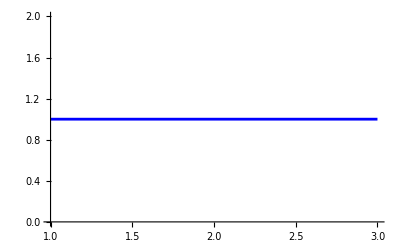

```mathematica
plotvexact=Plot[v[x]/.s,{x,xmin,xmax},PlotStyle->Blue]
```

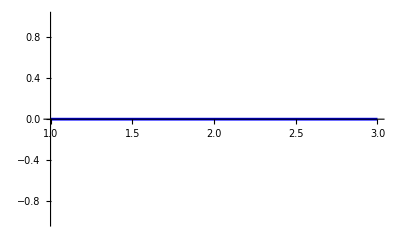

```mathematica
plotwexact=Plot[w[x]/.s,{x,xmin,xmax},PlotStyle->Blue]
```

```mathematica
plotσexact=Plot[σ[x]/.s,{x,xmin,xmax},PlotStyle->Blue]
```

-Graphics-

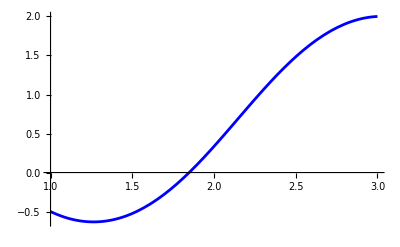

```mathematica
plotψexact=Plot[ψ[x]/.s,{x,xmin,xmax},PlotStyle->Blue]
```

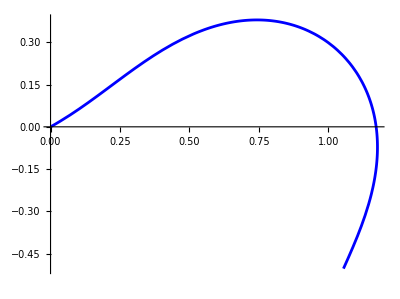

```mathematica
plotXexact=ParametricPlot[{X1[x],X2[x]}/.s,{x,xmin,xmax},PlotStyle->Blue]
```

```mathematica
(*check FE solution*)
```

```mathematica
(*check v*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/v.csv"];
t=Table[{t[[i,4]],t[[i,1]]},{i,2,Length[t]}]
```

Import::nffil: File /Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/v.csv not found during Import.

{}

```mathematica
plotvnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

-Graphics-

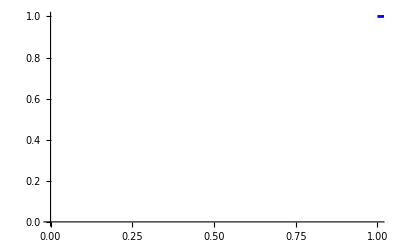

```mathematica
Show[plotvnum,plotvexact]
```

```mathematica
(*check w*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/w.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

Import::nffil: File /Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/w.csv not found during Import.

{}

```mathematica
plotwnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

-Graphics-

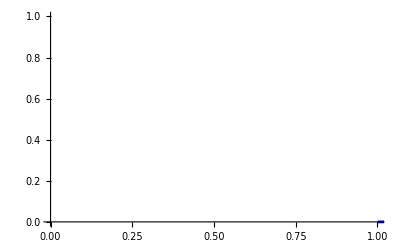

```mathematica
Show[plotwnum,plotwexact]
```

```mathematica
(*check sigma*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/sigma.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

Import::nffil: File /Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/sigma.csv not found during Import.

{}

```mathematica
plotσnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

-Graphics-

```mathematica
Show[plotσnum,plotσexact]
```

-Graphics-

```mathematica
(*check ψ*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/psi.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

Import::nffil: File /Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/psi.csv not found during Import.

{}

```mathematica
plotψnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

-Graphics-

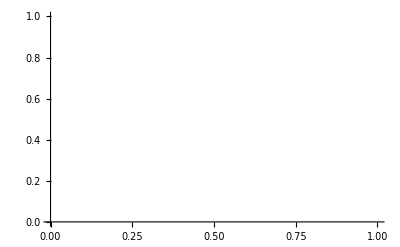

```mathematica
Show[plotψnum,plotψexact]
```

```mathematica
(*check X*)
```

```mathematica
tX=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/X.csv"];
tX=Table[{tX[[i,1]],tX[[i,2]]},{i,2,Length[tX]}]
```

Import::nffil: File /Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/X.csv not found during Import.

{}

```mathematica
plotXnum=ListPlot[tX,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

-Graphics-

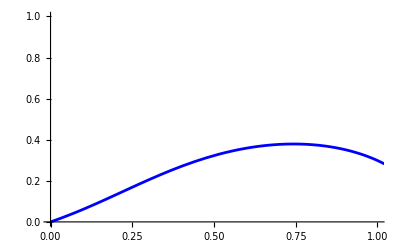

```mathematica
Show[plotXnum,plotXexact]
```